## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

NotebookDirectory::nosv: The notebook c8gdu_shm is not saved.

SetDirectory::fstr: File specification $Failed is not a string of one or more characters.

```mathematica
Column@Table[ToString@i<>".  ",{i,21}]
```

1.  
2.  
3.  
4.  
5.  
6.  
7.  
8.  
9.  
10.  
11.  
12.  
13.  
14.  
15.  
16.  
17.  
18.  
19.  
20.  
21.

```mathematica
niceForm[{x_,y_}]:=TraditionalForm[x î + y ĵ]
niceForm[{x_,y_,z_}] := TraditionalForm[x î + y ĵ+z k̂]
```

```mathematica
ihat:={0,1}; ihat3:={1,0,0};
jhat:={1,0}; jhat3:={0,1,0};
khat3:={0,0,1};
```

## Quiz

```mathematica
a=3ihat3+4jhat3+5khat3;
b=3ihat3;
```

```mathematica
N@Norm[a+b]
```

8.77496

```mathematica
niceForm[a×b]
```

15 ĵ-12 k̂

```mathematica
niceForm[Normalize[a×b]]
```

(5 ĵ)/(√41)-(4 k̂)/(√41)

## Rollercoaster 1

```mathematica
parallel[x_/;NumericQ[x],f_]:=Normalize[{1,f'[x]}]
perp[x_/;NumericQ[x],f_]:=Normalize[{-f'[x],1}]
```

```mathematica
contactPoint[{x_,y_},f_]:=FindMinimum[(parallel[x0,f].{x-x0,y-f[x0]})^2,{x0,x}]
```

```mathematica
gShow[{x_,y_},f_
```

```mathematica
Quiet@contactPoint[{1,2},Cos]/.{_,{_->x1_}}->x1
```

FindMinimum::nrlnum: The function value {1.41421 (0.-0.643852 (-0.540302+y))} is not a list of real numbers with dimensions {1} at {x0,x} = {1.,1.}.

0.482742

```mathematica
func:=Sin
```

```mathematica
Manipulate[Show[Plot[func[h],{h,-5,5},PlotRange->{-5,5},AspectRatio->1],x0=contactPoint[{x,y},func]/.{_,{_->x1_}}->x1;Graphics[{PointSize->Large,Point[{x,y}],Point[{x0,func[x0]}]}]],{x,-5,5},{y,-5,5}]
```

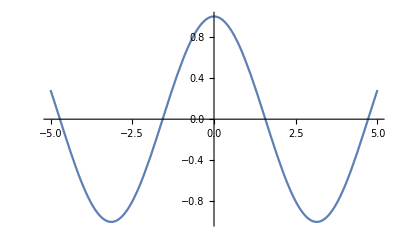

```mathematica
Plot[Cos[t],{t,-5,5}]
```

```mathematica
x0=contactPoint[{1,2},Cos]/.{_,{_->x1_}}->x1;Point[{x0,Cos[x0]}]
```

FindMinimum::nrlnum: The function value {1.41421 (0.-0.643852 (-0.540302+y))} is not a list of real numbers with dimensions {1} at {x0,x} = {1.,1.}.

Point[{0.482742,0.885725}]

```mathematica
x0
```

FindMinimum::nrlnum: The function value {1.41421 (0.-0.643852 (-0.540302+y))} is not a list of real numbers with dimensions {1} at {x0,x} = {1.,1.}.

FindMinimum[(parallel[x0,Cos].{x-x0,y-Cos[x0]})^2,{x0,x}]→0.482742

```mathematica
contactPoint[{1,2},Cos][[2,1]]
```

FindMinimum::nrlnum: The function value {1.41421 (0.-0.643852 (-0.540302+y))} is not a list of real numbers with dimensions {1} at {x0,x} = {1.,1.}.

General::stop: Further output of FindMinimum::nrlnum will be suppressed during this calculation.

(FindMinimum[(parallel[x0,Cos].{x-x0,y-Cos[x0]})^2,{x0,x}]→0.482742)→0.482742